```mathematica
(* Potential, without normalization *)
V[ϕ_] = ϕ^4;

(* Putting in required known constants *)
M = 1.2209*10^19 ; (*Non-reduced Planck Mass in GeV/c^2 *)
δ = 4.5*10^-5 ;(*I think this is the current value I'm using*)

(* Slow-roll parameters *)
H[ϕ_]=√((8 π)/(3 M^2)V[ϕ])
ϵ[ϕ_] = M^2/(4 π)(H'[ϕ]/H[ϕ])^2
(* Field Value at the end of inflation *)
ϕe = Re[x/. FindRoot[ϵ[x]==1,{x,M/√π}]]
Nume[ϕ_?NumberQ]:=Re[(8 π/M^2) NIntegrate[V[x]/V'[x],{x, ϕe,ϕ}]]

(* Field value NN e-folds before the end of inflation. Exact answer: *)
ϕN[NN_] := Re[x/. FindRoot[Nume[x] == NN, {x,ϕe}]]

(* Normalization *)
Vend[NN_]:= (3 δ^2 M^6)/(128π)(V'[ϕN[NN]]/V[ϕN[NN]])^2(V[ϕe]/V[ϕN[NN]])

(* Reheat Temperature *)
Trh[NN_]:=Vend[NN]^(1/4)

(* Max N *)
NM = Re[x/. FindRoot[x-Log[Trh[x]/M]==68,{x,60}]]
```

2.37071×10^-19 √(ϕ^4)

(4.74472×10^37)/ϕ^2

6.88819×10^18

127.815

```mathematica
ϕN[60]
```

5.37985×10^19

```mathematica
Vend[60]
```

7.43339×10^61

```mathematica
(Vend[60])^(1/4)
```

2.93628×10^15

```mathematica
Trh[60]
```

2.93628×10^15

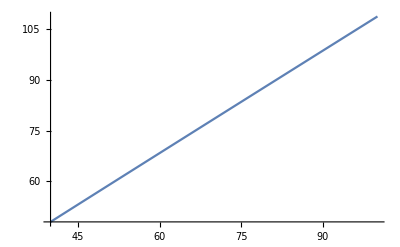

Syntax::bktmop: Expression "x-Log[Trh[x]/M],{x,40,100}]" has no opening "[".

```mathematica
Plot[x-Log[Trh[x]/M],{x,40,100}]
```

```mathematica
NSolve[x-Log[Trh[x]/M]==68, x]
```

{{x→127.815}}

```mathematica
x/.{x->{127.81487882613234,127.81487882613234}}
```

{127.815,127.815}

```mathematica
fff[x_] := x-Log[Trh[x]/M] 
fff[59.67]
```

67.9987

```mathematica
NSolve[fff[x]  == 68, x]
```

{{x→127.815}}

```mathematica
59.67 * 2.1415926
```

127.789

```mathematica
fff
```

```mathematica
fff[62.3326]
```

70.6935